16

{{-5,1/24},{-35/8,64/1201},{-15/4,16/229},{-25/8,64/681},{-5/2,4/31},{-15/8,64/361},{-5/4,16/69},{-5/8,64/241},{0,1/4},{5/8,64/321},{5/4,16/109},{15/8,64/601},{5/2,4/51},{25/8,64/1081},{15/4,16/349},{35/8,64/1761},{5,1/34}}

0.10719

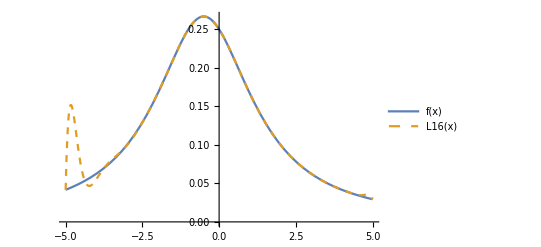

```mathematica
f[x_]:=1/(4+x+x^2)
n = 16
point = Table[{-5+(10*i)/n,f[-5+(10*i)/n]},{i,0,n,1}]
poly[x_]:= InterpolatingPolynomial[point,x]
error[x_] := f[x]-poly[x]
Max[Abs[Table[error[x],{x,-5,5,0.02}]]]
Plot[{f[x],poly[x]},{x,-5,5},PlotStyle->{Thick,Dashed},PlotLegends->{"f(x)","L16(x)"}]
```